```mathematica
SetOptions[MatrixPlot,PlotRange->{0,1},ColorFunction->GrayLevel,FrameTicks->False];
(* x -> a number represented as a string of n digits *)
df[n_,x_]:=StringJoin[ToString/@Join[ConstantArray[0,n-Floor@Log[10,x]-1],IntegerDigits[x]]]
```

```mathematica
(*img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/scream.jpeg"]];*)
img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/foliebergere.jpeg"]];
```

## Forward Euler Algorithm

Heat equation with the simplest algorithm: Explicit Forward Euler

```mathematica
L=1.;
len=20;
dx=L/len;
σ=L/6;
T=4 L^2;
steps=800; (* how many timesteps in the evolution *)
dt=dx^2/20;
T=dt * steps;
outfigs=10; (* number of figures generated, not all time steps are saved; this number cannot be equal to timesteps *)
outstep=steps/outfigs;
```

```mathematica
Print[dt," ",dx]
Print[T] (* how many integral times in the simulation *)
```

0.000125 0.05

0.1

```mathematica
(* initial data, selecting all color channels *)
data=img[[1;;;;10,1;;;;10]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
(* gaussian initial data, for tests *)
(*data=Partition[Exp[-(#1^2+#2^2)/(2 σ^2)]&@@@Tuples[Range[-L/2,L/2-dx,dx],2],len];*)
```

```mathematica
(* one step of the Forward Euler algorithm *)
FwdEuler[data_]:=data+dt/dx^2(RotateLeft[data,{0,1,0}]+RotateLeft[data,{0,-1,0}]+RotateLeft[data,{1,0,0}]+RotateLeft[data,{-1,0,0}]-4 data);
```

```mathematica
(* generates figures and saves them to plots, the output of this cell is the total time for the evaluation *)
(plots=Reap[Do[Sow[data=FwdEuler[data],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

{2.98032,{{1},198,{{{0.558415,0.341039,0.179776},{0.560254,0.340484,0.181945},{0.56263,0.340276,0.184355},115,{0.556495,0.343134,0.176232},{0.557152,0.341928,0.177868}},153,{{1},118,{1}}}}}
 |  |  |  |

```mathematica
(* save the images, change the path as appropriate to your computer *)
Export["/home/gabriel/Documents/HeatAnimation/scream_fwdeuler/scream_fwdeuler_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```

## Alternating Direction Implicit Method

Heat equation with an implicit algorithm and alternating direction

```mathematica
L=1.;
lenx=20;
leny=20;
dx=L/lenx;
dy=L/leny;
σ=L/6;
steps=200;
dt=dx^2/4;
T=dt * steps;
outfigs=100; (* must be smaller than steps *)
outstep=steps/outfigs;
```

```mathematica
Print[dt," ",dx]
Print[T] (* how many integral times in the simulation *)
```

0.000625 0.05

0.125

```mathematica
sizeReduce=5;(* the larger this number, the smaller the final figures are *)
```

```mathematica
(* limit is roughly 300x300 *)
With[{s=Dimensions[img]},lenx=Ceiling[s[[1]]/sizeReduce];leny=Ceiling[s[[2]]/sizeReduce];Print["Final image size: ",lenx,"x",leny]]
```

Final image size: 310x240

```mathematica
ADI[data_,By_,Bx_]:=Block[{phi},
phi=(2/dt-2/dx^2)data+1/dx^2 RotateLeft[data,{0,1}]+1/dx^2 RotateLeft[data,{0,-1}];
phi=Transpose[LinearSolve[By,#]&/@Transpose[phi]];
phi=(2/dt-2/dx^2)phi+1/dx^2 RotateLeft[phi,{1,0}]+1/dx^2 RotateLeft[phi,{-1,0}];
LinearSolve[Bx,#]&/@phi]
```

```mathematica
(*data=Partition[Exp[-(#1^2+#2^2)/(2 σ^2)]&@@@Tuples[{Range[-L/2,L/2-dx,dx],Range[-L/2,L/2-dy,dy]}],leny];*)
```

```mathematica
(* matrices for the implicit method, one corresponds to the y half-step, another to the x half-step *)
By=SparseArray[{{i_,i_}->2/dt+2/dx^2,{i_,j_}/;Abs[i-j]==1->-1/dx^2},{lenx,lenx}];
Bx=SparseArray[{{i_,i_}->2/dt+2/dx^2,{i_,j_}/;Abs[i-j]==1->-1/dx^2},{leny,leny}];
```

```mathematica
data=img[[1;;;;sizeReduce,1;;;;sizeReduce,1]];
```

```mathematica
(* if True, the dimensions are correct *)
With[{s=Dimensions@data},TrueQ[s[[1]]==lenx && s[[2]]==leny]]
```

True

```mathematica
(plots1=Reap[Do[Sow[data=ADI[data,By,Bx],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

44.0969

```mathematica
data=img[[1;;;;sizeReduce,1;;;;sizeReduce,2]];
```

```mathematica
(plots2=Reap[Do[Sow[data=ADI[data,By,Bx],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

42.6543

```mathematica
data=img[[1;;;;sizeReduce,1;;;;sizeReduce,3]];
```

```mathematica
(plots3=Reap[Do[Sow[data=ADI[data,By,Bx],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

53.2834

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/scream_adim/scream_adim_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image[Transpose[{plots1[[#]],plots2[[#]],plots3[[#]]},{3,1,2}]]]&/@Range[Length@plots1];
```

## Forward Euler Algorithm for the Wave Equation

Wave equation with the Explicit Forward Euler algorithm
See notes about the initial conditons on: https://www.uni-muenster.de/Physik.TP/archive/fileadmin/lehre/NumMethoden/WS1011/script1011Wave.pdf
Here, I choose u(x,t=0) = image, u_t(x,t=0) = 0

```mathematica
(* https://www.uni-muenster.de/Physik.TP/archive/fileadmin/lehre/NumMethoden/WS1011/script1011Wave.pdf *)
```

```mathematica
len=20;
dx=1.;
σ=L/6;
T=4 L^2;
steps=2000;
dt=dx^2/1000;
T=dt * steps;
outfigs=10;
outstep=steps/outfigs;
```

```mathematica
Print[dt," ",dx]
Print[T] (* how many integral times in the simulation *)
```

0.001 1.

2.

```mathematica
data=img[[1;;;;4,1;;;;4,2]];
```

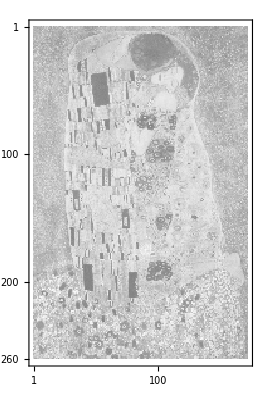

```mathematica
MatrixPlot@data
```

```mathematica
data//Dimensions
```

{260,171}

```mathematica
(*data=Partition[Exp[-(#1^2+#2^2)/(2 σ^2)]&@@@Tuples[Range[-L/2,L/2-dx,dx],2],len];*)
```

```mathematica
data=Join[{data,data+dt^2/(2 dx^2)(RotateLeft[data,{0,1}]+RotateLeft[data,{0,-1}]+RotateLeft[data,{1,0}]+RotateLeft[data,{-1,0}]-4 data)}];
```

```mathematica
FwdEulerWave[data_]:=Join[{data[[2]],-data[[1]]+2data[[2]]+dt/dx^2(RotateLeft[data[[2]],{0,1}]+RotateLeft[data[[2]],{0,-1}]+RotateLeft[data[[2]],{1,0}]+RotateLeft[data[[2]],{-1,0}]-4 data[[2]])}];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=FwdEulerWave[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

6.92051

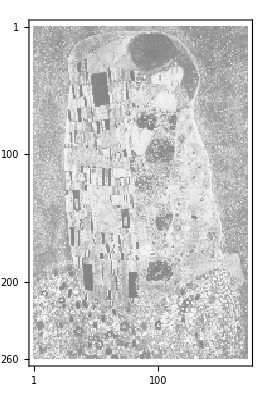
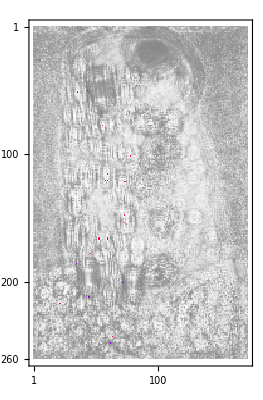
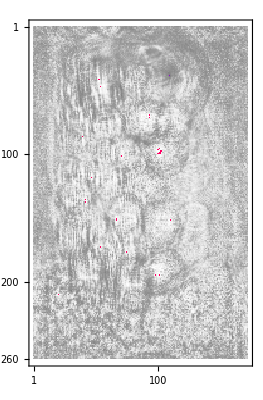
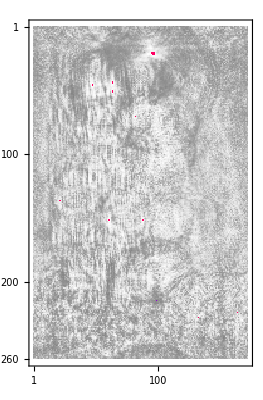
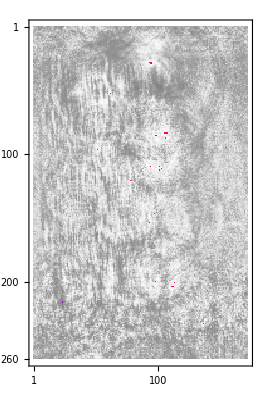
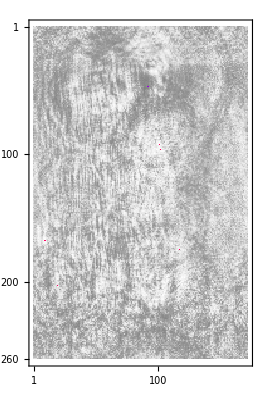
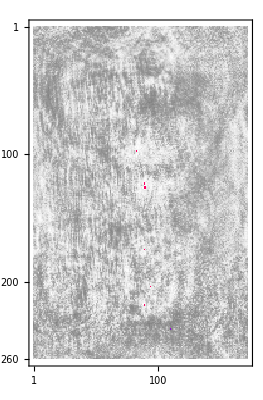
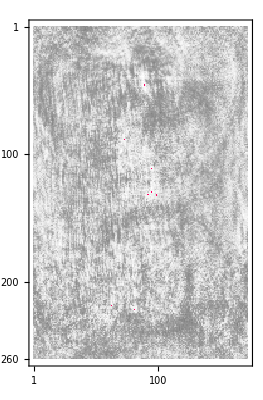

```mathematica
MatrixPlot/@plots
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/scream_fwdeuler/scream_fwdeuler_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```

## Forward Euler Algorithm for the Wave Equation, all color channels

```mathematica
(* https://www.uni-muenster.de/Physik.TP/archive/fileadmin/lehre/NumMethoden/WS1011/script1011Wave.pdf *)
```

```mathematica
len=20;
dx=1.;
σ=L/6;
T=4 L^2;
steps=2000;
dt=dx^2/1000;
T=dt * steps;
outfigs=100;
outstep=steps/outfigs;
```

```mathematica
Print[dt," ",dx]
Print[T] (* how many integral times in the simulation *)
```

0.001 1.

2.

```mathematica
data=img[[1;;;;4,1;;;;4]];
```

```mathematica
Image@data
```

-Graphics-

```mathematica
data//Dimensions
```

{325,214,3}

```mathematica
(*data=Partition[Exp[-(#1^2+#2^2)/(2 σ^2)]&@@@Tuples[Range[-L/2,L/2-dx,dx],2],len];*)
```

```mathematica
data=Join[{data,data+dt^2/(2 dx^2)(RotateLeft[data,{0,1,0}]+RotateLeft[data,{0,-1,0}]+RotateLeft[data,{1,0,0}]+RotateLeft[data,{-1,0,0}]-4 data)}];
```

```mathematica
FwdEulerWave[data_]:=Join[{data[[2]],-data[[1]]+2data[[2]]+dt/dx^2(RotateLeft[data[[2]],{0,1,0}]+RotateLeft[data[[2]],{0,-1,0}]+RotateLeft[data[[2]],{1,0,0}]+RotateLeft[data[[2]],{-1,0,0}]-4 data[[2]])}];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=FwdEulerWave[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

36.9614

```mathematica
Image/@plots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/kiss_wave/kiss_fwdewave_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=FwdEulerWave[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

36.8171

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/kiss_wave/kiss_fwdewave_"<>df[Floor@Log[10,steps]+1,steps+#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```

## 2nd order Adams-Bashforth for the KPZ equation

Adams-Bashforth method (explicit 2nd order method) for the KPZ equation (a nonlinear equation)

```mathematica
len=20;
dx=1.;
σ=10 dx;
steps=1000;
dt=dx^2/1000;
T=dt * steps;
outfigs=10;
outstep=steps/outfigs;
nu=1.;
lambda=30.;
r=30.
```

30.

```mathematica
Print[dt," ",dx]
Print[T] (* how many integral times in the simulation *)
```

0.001 1.

1.

```mathematica
data=img[[1;;;;4,1;;;;4,All]];
```

```mathematica
data//Dimensions
```

{192,256,3}

```mathematica
One=ConstantArray[1,data//Dimensions];
```

```mathematica
KPZ2[data_]:=nu/dx^2(RotateLeft[data,{0,1,0}]+RotateLeft[data,{0,-1,0}]+RotateLeft[data,{1,0,0}]+RotateLeft[data,{-1,0,0}]-4 data)+lambda/(4 dx^2)(RotateLeft[data,{0,1,0}]-RotateLeft[data,{0,-1,0}])^2+lambda/(4 dx^2)(RotateLeft[data,{1,0,0}]-RotateLeft[data,{-1,0,0}])^2
KPP[data_]:=nu/dx^2(RotateLeft[data,{0,1,0}]+RotateLeft[data,{0,-1,0}]+RotateLeft[data,{1,0,0}]+RotateLeft[data,{-1,0,0}]-4 data)+r data(One-data)
```

```mathematica
(* Euler step *)
data=Join[{data,data+dt KPZ2[data]}];
```

```mathematica
data//Dimensions
```

{2,192,256,3}

```mathematica
AB2[data_]:=With[{s=data[[2]]+1.5 dt KPZ2[data[[2]]]-.5 dt KPZ2[data[[1]]]},Join[{data[[2]],If[Max[s]>1,s/Max[s],s]}]];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=AB2[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

138.754

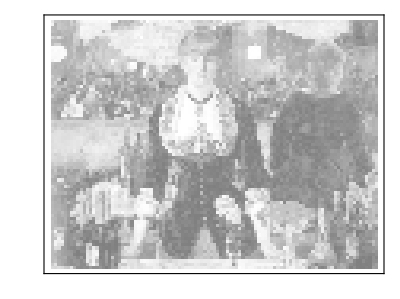
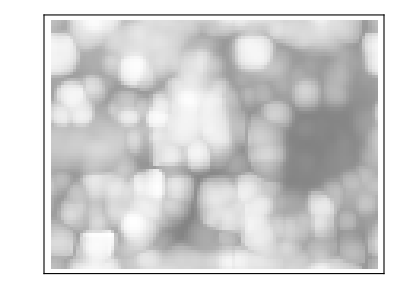
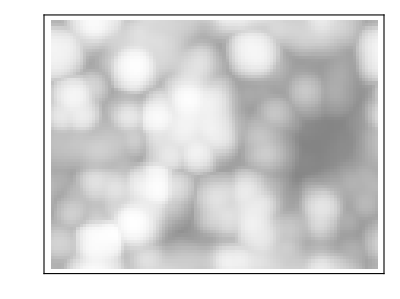
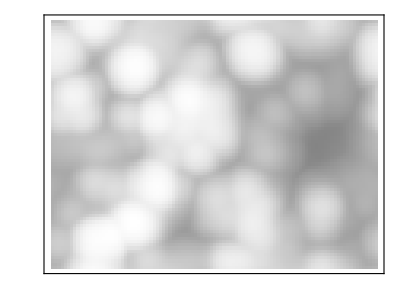
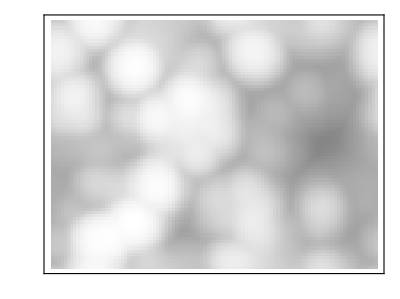
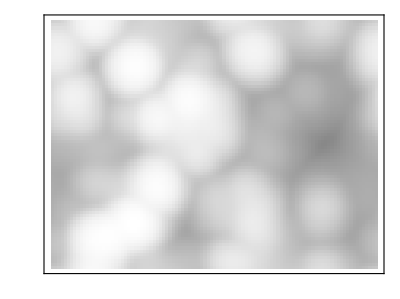
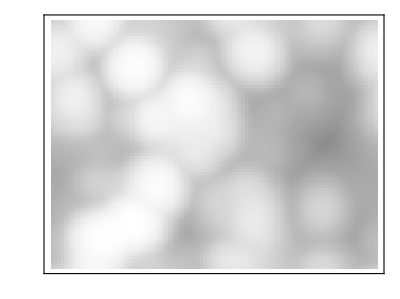
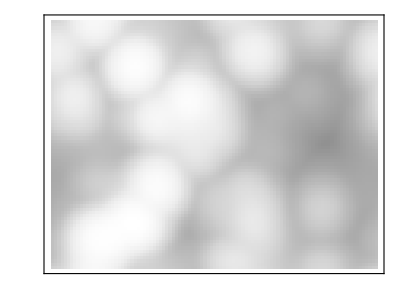

```mathematica
MatrixPlot/@plots
```

```mathematica
Max[plots]
```

1.

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/folie/folie_fwdekpz_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```

### KPP (Fisher)

```mathematica
(* Euler step *)
data=Join[{data,data+dt KPP[data]}];
```

```mathematica
data//Dimensions
```

{2,192,256,3}

```mathematica
AB2[data_]:=With[{s=data[[2]]+1.5 dt KPP[data[[2]]]-.5 dt KPP[data[[1]]]},Join[{data[[2]],If[Max[s]>1,s/Max[s],s]}]];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=AB2[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

29.4295

```mathematica
Image/@plots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Max/@plots
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/folie/folie_fwdekpz_"<>df[Floor@Log[10,steps]+1,outfigs+#]<>".png",Image@plots[[#]]]&/@Range[Length@plots];
```